# Quantile Regression instead of ARIMA

## Wolfram Language version

Anton Antonov 
December 2024

## Setup

Load the paclets “MonadicQuantileRegression” and “DataReshapers”:

```mathematica
Needs["AntonAntonov`MonadicQuantileRegression`"];
Needs["AntonAntonov`DataReshapers`"];
Needs["AntonAntonov`NLPTemplateEngine`"]
```

```mathematica
(*Concretize[" make a quanta regression pipeline using the data dfTemperature with the basis bFuncs and probility 0.5"]*)
```

### Temperature data

```mathematica
url="https://raw.githubusercontent.com/antononcube/MathematicaVsR/master/Data/MathematicaVsR-Data-Atlanta-GA-USA-Temperature.csv";
dfTemperature=Import[url,"Dataset"];
```

```mathematica
dfTemperature
```

Dataset[<>]

```mathematica
dfTemperature=dfTemperature[Select[2020≤DateList[#AbsoluteTime][[1]]≤2023&]];
```

Prepare the data for QRMon pipelines:

```mathematica
dfTemperature=dfTemperature[All,{"AbsoluteTime","Temperature"}];
RandomSample[dfTemperature,3]
```

```mathematica
data=Normal@dfTemperature[Values];
```

## First fits

Over the data “as is”:

Data summary:  {1 Regressor
Min | 3786825600
1st Qu | 3818340000
Mean | 3849897600
Median | 3849897600
3rd Qu | 3881455200
Max | 3912969600,2 Value
Min | -11.89
1st Qu | 10.06
Mean | 15.8553
Median | 16.94
3rd Qu | 22.5725
Max | 32.39}

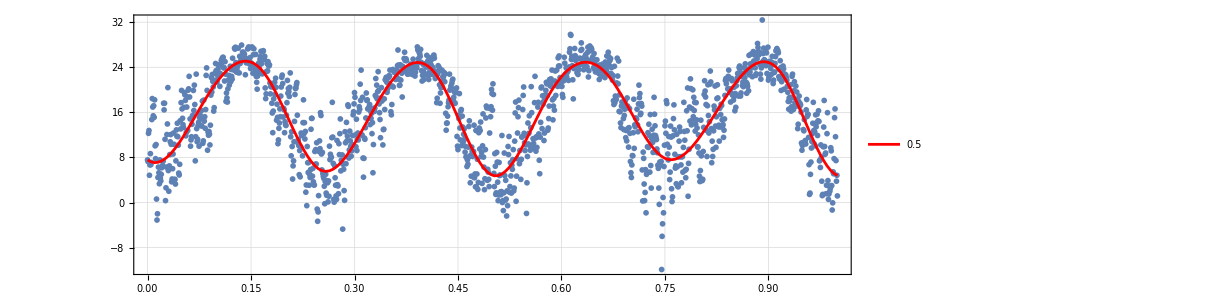
Plot:  -Graphics-

{0.386885,Null}

```mathematica
AbsoluteTiming[
obj=
QRMonUnit[data]⟹
QRMonEchoDataSummary[]⟹
QRMonRescale["Axes"->{True,False}]⟹
QRMonQuantileRegression[12,0.5]⟹
QRMonSetRegressionFunctionsPlotOptions[{PlotStyle->Red}]⟹
QRMonPlot["DateListPlot"->False,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->900];
]
```

The data rescaled over both dimensions:

Data summary:  {1 Regressor
Min | 3786825600
1st Qu | 3818340000
Mean | 3849897600
Median | 3849897600
3rd Qu | 3881455200
Max | 3912969600,2 Value
Min | -11.89
1st Qu | 10.06
Mean | 15.8553
Median | 16.94
3rd Qu | 22.5725
Max | 32.39}

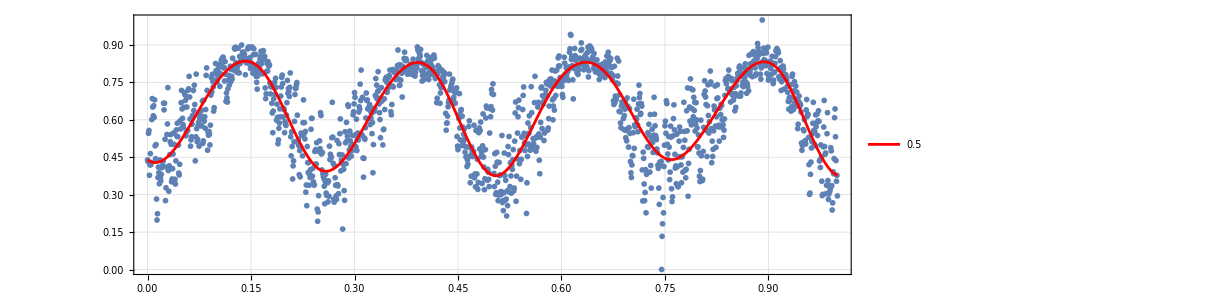
Plot:  -Graphics-

{0.41702,Null}

```mathematica
AbsoluteTiming[
obj=
QRMonUnit[data]⟹
QRMonEchoDataSummary[]⟹
QRMonRescale["Axes"->{True,True}]⟹
QRMonQuantileRegression[12,0.5]⟹
QRMonSetRegressionFunctionsPlotOptions[{PlotStyle->Red}]⟹
QRMonPlot["DateListPlot"->False,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->900];
]
```

## Search for Cos and Sin model

187

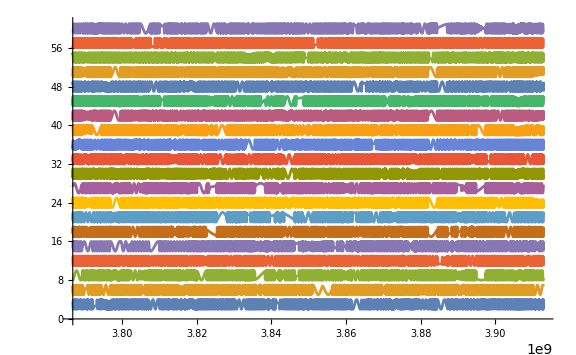

```mathematica
bFuncs=Prepend[Flatten[Table[{Sin[b+h x],Cos[b+h x]},{h,20,23,0.1},{b,0,1,0.5}]],1];
Length[bFuncs]
Block[{n=20},
Plot[Evaluate[MapThread[Plus,{RandomSample[bFuncs,n],3Range[1,n]}]],{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]},ImageSize->Large]
]
```

57

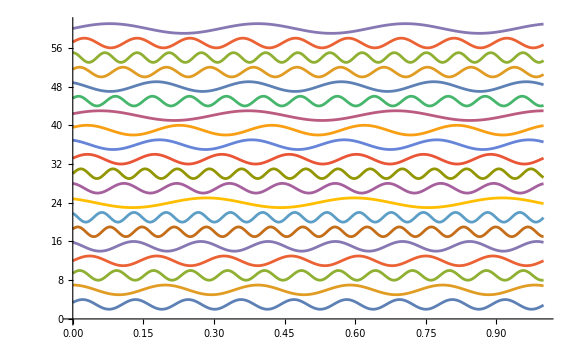

```mathematica
bFuncs=Prepend[Flatten[Table[{Sin[b+h x],Cos[b+h x]},{h,20,100,12},{b,0,π/4,0.2}]],1];
Length[bFuncs]
Block[{n=20},
Plot[Evaluate[MapThread[Plus,{RandomSample[bFuncs,n],3Range[1,n]}]],{x,0,1},ImageSize->Large]
]
```

## Fit with a large basis of functions

Let us demonstrate:

Rescaling the data

Using function basis with infinite support

The latter allows using Quantile Regression with Autoregressive Integrated Moving Average (ARIMA).

```mathematica
bFuncs=Prepend[Flatten[Table[With[{b=b,h=h},{Sin[b+h*#]&,Cos[b+h*#]&}],{h,20,32,2},{b,0,2π,0.25}]],1&];
Length[bFuncs]
```

365

```mathematica
Manipulate[
Plot[Sin[b+h*x],{x,0,1}],
{h,10,40,0.1,Appearance->"Open"},
{b,0,2π,0.1,Appearance->"Open"}
]
```

Data summary:  {1 Regressor
Min | 3786825600
1st Qu | 3818340000
Mean | 3849897600
Median | 3849897600
3rd Qu | 3881455200
Max | 3912969600,2 Value
Min | -11.89
1st Qu | 10.06
Mean | 15.8553
Median | 16.94
3rd Qu | 22.5725
Max | 32.39}

Data summary:  {1 Regressor
Min | 0
1st Qu | 0.249829
Mean | 0.5
Median | 0.5
3rd Qu | 0.750171
Max | 1,2 Value
Min | 0.
1st Qu | 0.495709
Mean | 0.626589
Median | 0.651084
3rd Qu | 0.778286
Max | 1.}

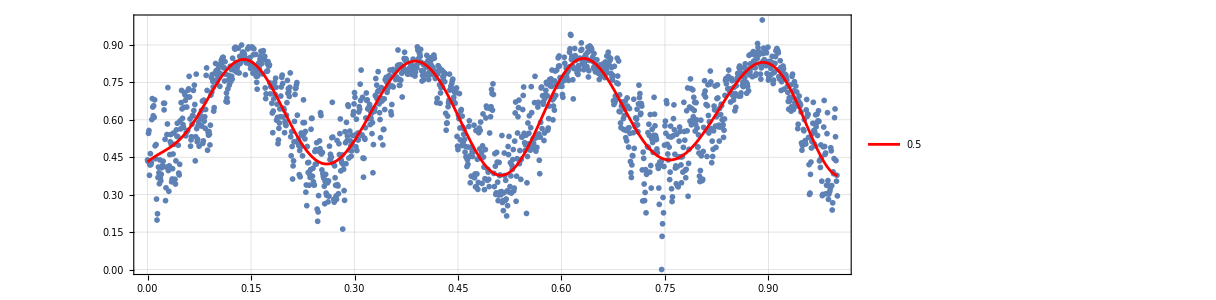
Plot:  -Graphics-

{21.0807,Null}

```mathematica
AbsoluteTiming[
obj=
QRMonUnit[Normal@dfTemperature[Values]]⟹
QRMonEchoDataSummary[]⟹
QRMonRescale["Axes"->{True,True}]⟹
QRMonEchoDataSummary[]⟹
QRMonQuantileRegressionFit[Through[bFuncs[x]],0.5,Method->{LinearProgramming,Method->"InteriorPoint",Tolerance-> 0.01}]⟹
QRMonSetRegressionFunctionsPlotOptions[{PlotStyle->Red}]⟹
QRMonPlot["DateListPlot"->False,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->900];
]
```

## Most significant components

```mathematica
qFunc2=(obj⟹QRMonTakeRegressionFunctions)[0.5][t];
```

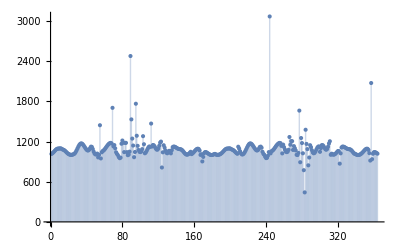

{{3071.41,Sin[2.25+24 t]},{2479.78,Cos[2.5+26 t]},{2076.31,Sin[4.5+32 t]},{1766.63,Cos[4.+26 t]},{1705.38,Cos[4.+24 t]},{1663.91,Sin[4.+26 t]},{1532.53,Cos[2.75+26 t]},{1470.1,Cos[1.75+28 t]},{1445.15,Cos[0.5+24 t]},{1377.66,Sin[5.75+26 t]},{1287.93,Cos[4.25+26 t]},{1281.5,Cos[6.+26 t]},{1269.15,Sin[1.25+26 t]},{1253.76,Sin[4.5+26 t]},{1245.65,Cos[3.+26 t]}}

```mathematica
terms=Cases[qFunc2,(f_?NumberQ*c_):>{f,c}];
ListPlot[terms⟦All,1⟧,PlotRange->All,Filling->Axis]
TakeLargestBy[terms,Abs@*First,UpTo[15]]
```

```mathematica
qFunc2Chopped=Total@Cases[qFunc2,(f_?NumberQ*c_)/;Abs[f]>=10^-6];
```

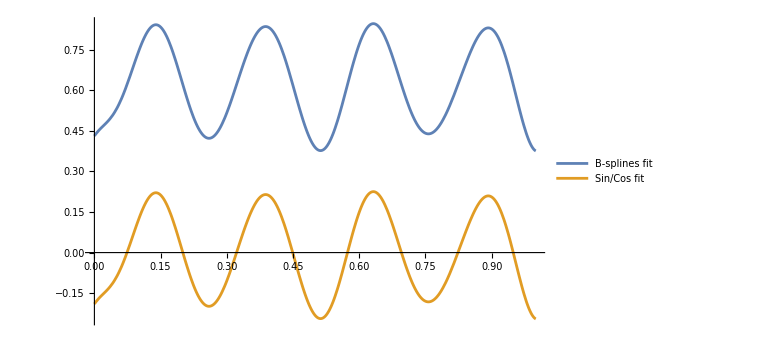

```mathematica
Plot[Evaluate[{qFunc2,qFunc2Chopped}],{t,0,1},PlotLegends->{"B-splines fit","Sin/Cos fit","Chopped Sin/Cos fit"},PlotRange->All,ImageSize->Large]
```

## Extension

Fit with the smaller basis:

```mathematica
largestTerms=TakeLargestBy[terms,First,8]
```

{{3071.41,Sin[2.25+24 t]},{2479.78,Cos[2.5+26 t]},{2076.31,Sin[4.5+32 t]},{1766.63,Cos[4.+26 t]},{1705.38,Cos[4.+24 t]},{1663.91,Sin[4.+26 t]},{1532.53,Cos[2.75+26 t]},{1470.1,Cos[1.75+28 t]}}

```mathematica
freqs=Cases[largestTerms⟦All,2⟧,f_?NumberQ*t:>f,∞]
```

{24,26,32,26,24,26,26,28}

Data summary:  {1 Regressor
Min | 0
1st Qu | 0.249829
Mean | 0.5
Median | 0.5
3rd Qu | 0.750171
Max | 1,2 Value
Min | 0.
1st Qu | 0.495709
Mean | 0.626589
Median | 0.651084
3rd Qu | 0.778286
Max | 1.}

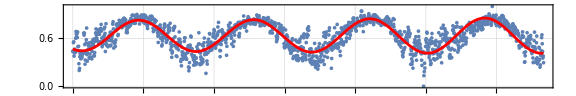
Plot:  -Graphics-

{1 column 1
Min | 0
1st Qu | 0.249829
Mean | 0.5
Median | 0.5
3rd Qu | 0.750171
Max | 1,2 column 2
Min | -0.418739
1st Qu | -0.0598751
Mean | -0.00170942
Median | 2.22045×10^-16
3rd Qu | 0.0579761
Max | 0.313938}

{0.313097,Null}

```mathematica
AbsoluteTiming[
qrObj3=
QRMonUnit[data]⟹
QRMonRescale[Axes->{True,True}]⟹
QRMonEchoDataSummary⟹
QRMonQuantileRegressionFit[Prepend[largestTerms⟦All,2⟧,1],0.5,Method->{LinearProgramming,Method->"CLP",Tolerance->10^-5}]⟹
QRMonSetRegressionFunctionsPlotOptions[{PlotStyle->Red}]⟹
QRMonPlot[PlotTheme->"Detailed",AspectRatio->1/6,ImageSize->Large]⟹
QRMonErrors["RelativeErrors"->False]⟹
QRMonEchoFunctionValue[RecordsSummary@*Last];
]
```

```mathematica
qFunc3=(qrObj3⟹QRMonTakeRegressionFunctions)[0.5][t];
```

```mathematica
qFunc3=FullSimplify[qFunc3]
```

0.632426+0.0385044 Cos[4.+24 t]+0.178022 Sin[4.+26 t]+0.00647981 Sin[4.5+32 t]

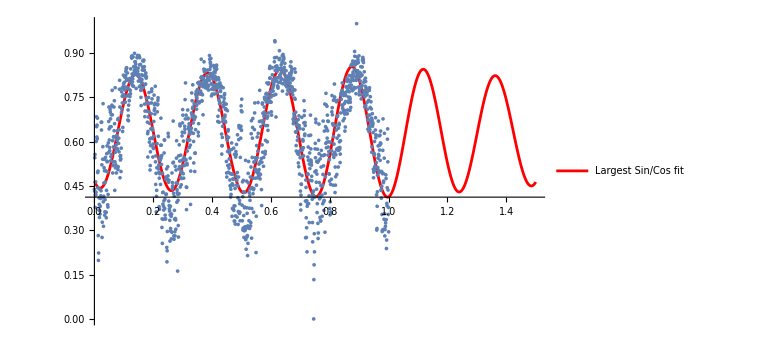

```mathematica
opts={PlotRange->All,ImageSize->Large};
Show[{
Plot[Evaluate[{qFunc3}],{t,0,1.5},PlotStyle->{Red},PlotLegends->{"Largest Sin/Cos fit"},Evaluate@opts],
ListPlot[qrObj3⟹QRMonTakeData]
}]
```